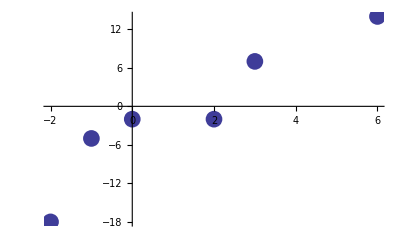

(-18 | 0 | 0 | 0 | 0 | 0
-5 | 13 | 0 | 0 | 0 | 0
-2 | 3 | -5 | 0 | 0 | 0
-2 | 0 | -1 | 1 | 0 | 0
7 | 9 | 3 | 1 | 0 | 0
14 | 7/3 | -5/3 | -7/9 | -16/63 | -2/63)

-18+13 (2+x)-5 (1+x) (2+x)+x (1+x) (2+x)-2/63 (-3+x) (-2+x) x (1+x) (2+x)

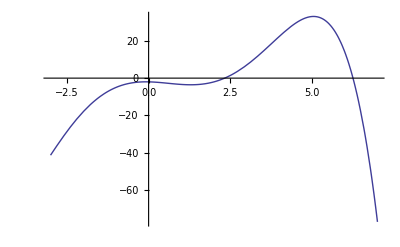

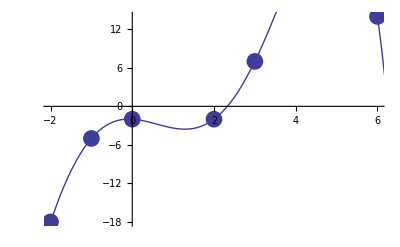

```mathematica
n=Input["Dame el grado del polinomio"];
MatrizX={};
MatrizY={};
MatrizV={};

For[i=1,i≤n+1,i++,
VariableX=Input["Introduzca X"<>ToString[i]];
AppendTo[MatrizX,VariableX];
VariableY=Input["Introduzca Y"<>ToString[i]];
AppendTo[MatrizY,VariableY];
];
Datos=Table[{MatrizX[[i]],MatrizY[[i]]},{i,1,n+1}];
Grafica1=ListPlot[Datos,PlotStyle->PointSize[0.03]]

For[i=1,i≤n+1,i++,
Renglon={};
For[j=1,j≤n+1,j++,
AppendTo[Renglon,0];
];
AppendTo[MatrizV,Renglon];
]
MatrizV//MatrixForm;

For[i=1,i≤n+1,i++,
MatrizV[[i,1]]=MatrizY[[i]]
]

For[i=2,i≤n+1,i++,
For[j=2,j≤i,j++,
MatrizV[[i,j]]=(MatrizV[[i,j-1]]-MatrizV[[i-1,j-1]])/(MatrizX[[i]]-MatrizX[[i-j+1]])
]
]
MatrizV//MatrixForm

suma=MatrizV[[1,1]];

For[i=2,i≤n+1,i++,
Producto=1;
For[j=1,j<i,j++,
Producto=Producto*(x-MatrizX[[j]])
];
suma=suma+Producto*MatrizV[[i,i]]
]
P[x_]=suma
Grafica2=Plot[P[x],{x,MatrizX[[1]]-1,MatrizX[[n+1]]+1},PlotStyle->PointSize[0.03]]
Show[Grafica1,Grafica2]
```